```mathematica
f[q_,x_]:=q^2/(I*p0+q^2/2-p^2+2*p*q*x-q^2+mϕ-mψ)
```

```mathematica
Integrate[f[q,x],x]
```

(q Log[mϕ-mψ-p^2+ⅈ p0-q^2/2+2 p q x])/(2 p)

```mathematica
g[x_]:=(q Log[mϕ-mψ-p^2+ⅈ p0-q^2/2+2 p q x])/(2 p)
```

```mathematica
Simplify[g[1]-g[-1]]
```

1/(2 p)q (-Log[mϕ-mψ-p^2+ⅈ p0-2 p q-q^2/2]+Log[mϕ-mψ-p^2+ⅈ p0+2 p q-q^2/2])

```mathematica
h[q_]:=1/(2 p)q (-Log[mϕ-mψ-p^2+ⅈ p0-2 p q-q^2/2]+Log[mϕ-mψ-p^2+ⅈ p0+2 p q-q^2/2])
```

```mathematica
Integrate[h[q],q]
```

-2 q-2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(2 p-q)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(2 p+q)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+((mϕ-mψ+3 p^2+ⅈ p0) Log[2 (mϕ-mψ-p^2+ⅈ p0)-4 p q-q^2])/(2 p)-((mϕ-mψ+3 p^2+ⅈ p0) Log[2 (mϕ-mψ-p^2+ⅈ p0)+4 p q-q^2])/(2 p)-(q^2 Log[mϕ-mψ-p^2+ⅈ p0-2 p q-q^2/2])/(4 p)+(q^2 Log[mϕ-mψ-p^2+ⅈ p0+2 p q-q^2/2])/(4 p)

```mathematica
k[q_]:=-2 q-2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(2 p-q)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(2 p+q)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+((mϕ-mψ+3 p^2+ⅈ p0) Log[2 (mϕ-mψ-p^2+ⅈ p0)-4 p q-q^2])/(2 p)-((mϕ-mψ+3 p^2+ⅈ p0) Log[2 (mϕ-mψ-p^2+ⅈ p0)+4 p q-q^2])/(2 p)-(q^2 Log[mϕ-mψ-p^2+ⅈ p0-2 p q-q^2/2])/(4 p)+(q^2 Log[mϕ-mψ-p^2+ⅈ p0+2 p q-q^2/2])/(4 p)
```

```mathematica
Limit[k[q],q->Sqrt[-2mϕ]]
```

-2 √2 √-mϕ-2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(-√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ-4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)-((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ+4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)+(mϕ Log[2 mϕ-mψ-2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p)-(mϕ Log[2 mϕ-mψ+2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p)

```mathematica
Limit[-2 √2 √-mϕ-2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(-√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ-4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)-((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ+4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)+(mϕ Log[2 mϕ-mψ-2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p)-(mϕ Log[2 mϕ-mψ+2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p),p->0]
```

-4 √2 (√-mϕ-√(mϕ-mψ+ⅈ p0) ArcTanh[(√-mϕ)/(√(mϕ-mψ+ⅈ p0))])

```mathematica
SelfEnergy[p0_,p_,mϕ_,mψ_]:=-2 √2 √-mϕ-2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(-√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+2 √2 √(mϕ-mψ+p^2+ⅈ p0) ArcTanh[(√2 √-mϕ+2 p)/(√2 √(mϕ-mψ+p^2+ⅈ p0))]+((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ-4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)-((mϕ-mψ+3 p^2+ⅈ p0) Log[2 mϕ+4 √2 √-mϕ p+2 (mϕ-mψ-p^2+ⅈ p0)])/(2 p)+(mϕ Log[2 mϕ-mψ-2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p)-(mϕ Log[2 mϕ-mψ+2 √2 √-mϕ p-p^2+ⅈ p0])/(2 p)
```

```mathematica
SelfEnergy0[p0_,mϕ_,mψ_]:=-4 √2 (√-mϕ-√(mϕ-mψ+ⅈ p0) ArcTanh[(√-mϕ)/(√(mϕ-mψ+ⅈ p0))])
```

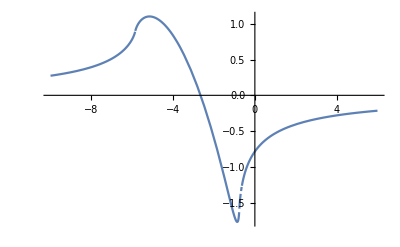

```mathematica
Plot[Re[SelfEnergy[I*p0-0.01,0.9,-1,0.5]],{p0,-10,6}, PlotRange->All]
```